1. Дана конечная струна длины L = 1, закрепленная на концах . Начальное смещение ноль и f (x, t) = 0. Начальная скорость представлена на рисунке . Построить профиль струны .

-Graphics-

```mathematica
stc[x_,w_] =( w/(2*Pi))* ArcCos[Cos[2*Pi*x/w]]
```

(w ArcCos[Cos[(2 π x)/w]])/(2 π)

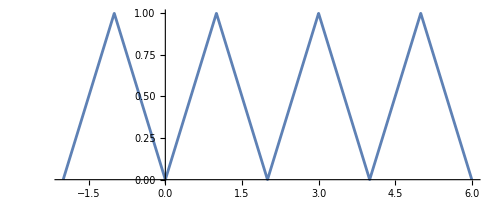

```mathematica
Plot[stc[x,2],{x,-2,6},AspectRatio->Automatic]
```

Пусть начальная скорость 0, кроме двух отрезков: [0.2;0.3] - скорость равна 1 и [0.7;0.8] - скорость равна -1 
Зададим кусочную функцию начальной скорости:

```mathematica
ψ[x_] = Piecewise[{{0,x<=0.2},{1,x<=0.3},{0,x<=0.7},{-1,x<=0.8}},0]
```

Piecewise[{{0, x≤0.2}, {1, x≤0.3}, {0, x≤0.7}, {-1, x≤0.8}, {0, True}}]

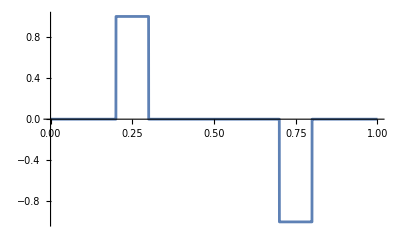

```mathematica
Plot[ψ[x],{x,0,1}, Exclusions->None]
```

```mathematica
a=.;v1[x_,t_]=1/(2*a)*Simplify[Integrate[ψ[τ],{τ,α,β},Assumptions:>α>0&&β>0]];
u1[x_,t_]=v1[x,t]/. {α->stc[x-a*t,2*L],β->stc[x+a*t,2*L]};
a=1;L=1;T=Range[0,1.98,0.02];
Animate[Plot[u1[x,t],{x,0,1},PlotRange->{-0.12,0.12},PlotLabel->t],{t,T},AnimationRunning->False]
```

2. Дана конечная струна длины L = 1, закрепленная на концах . В начальный момент начальная скорость равна нулю и f (x, t) = 0, а начальное отклонение представлено на рисунке. Построить профиль струны.

```mathematica
ϕ[x_] = Piecewise[{{0,x<=0.2},{5*x -1,x<=0.4},{-5*x +3,x<=0.8}},0 ]
```

Piecewise[{{0, x≤0.2}, {-1+5 x, x≤0.4}, {3-5 x, x≤0.8}, {0, True}}]

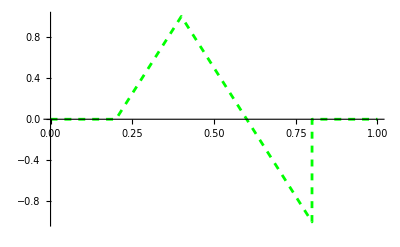

```mathematica
Plot[ϕ[x],{x,0,1}, Exclusions->None,  PlotStyle->{Green, Dashed}]
```

```mathematica
a=1; L = 1;
u2[x_,t_]:=(1/2)*((-1)^Floor[(x+a*t)/L]*ϕ[stc[x+a*t,2*L]]+(-1)^Floor[(x-a*t)/L]*ϕ[stc[x-a*t,2*L]])
T=Range[0,1.98,0.02];
```

```mathematica
T=Range[0,1.98,0.02];
```

```mathematica
Animate[Plot[u2[x,t],{x,0,1},PlotRange->{-1,1},PlotLabel->t],{t,T},AnimationRunning->False]
```

3. Дана конечная струна длины L = 1, закрепленная на концах . В начальный момент f(x, t) = 0, а начальное отклонение и скорость представлены на рисунке. Построить профиль струны.

Зададим функции скорости и отклонения отдельно:

```mathematica
ψ2[x_] = Piecewise[{{0,x<=0.2},{-1,x<=0.3}},0]
```

Piecewise[{{0, x≤0.2}, {-1, x≤0.3}, {0, True}}]

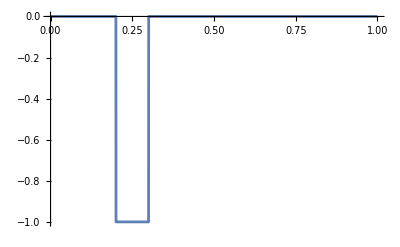

```mathematica
Plot[ψ2[x], {x,0,1}, Exclusions->None]
```

```mathematica
ϕ2[x_] = Piecewise[{{0,x<=0.6},{5x-3, x<=0.8}, {-5x+5,x<=1}}, 0]
```

Piecewise[{{0, x≤0.6}, {-3+5 x, x≤0.8}, {5-5 x, x≤1}, {0, True}}]

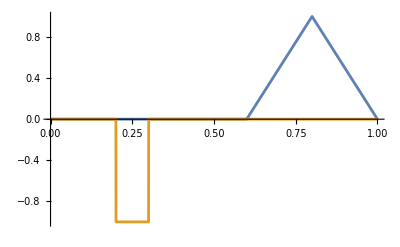

```mathematica
Plot[{ϕ2[x],ψ2[x]}, {x,0,1},  Exclusions->None, PlotRange->All]
```

```mathematica
v3[x_,t_]= 1/(2*a)*Simplify[Integrate[ψ2[τ],{τ,α,β},Assumptions:>α>0&&β>0]]; 
u3[x_,t_] = (1/2)*((-1)^Floor[(x+a*t)/L]*ϕ2[stc[x+a*t,2*L]]+(-1)^Floor[(x-a*t)/L]*ϕ2[stc[x-a*t,2*L]]) + (v3[x,t]/. {α->stc[x-a*t,2*L],β->stc[x+a*t,2*L]});
```

```mathematica
a=1; L = 1;
```

```mathematica
T=Range[0,1.98,0.02];
```

```mathematica
Animate[Plot[u3[x,t],{x,0,1},PlotRange->{-1,1},PlotLabel->t],{t,T},AnimationRunning->False]
```

Вывод:
1. На графиках функции u(x,t) мы видим, как возмущение, заданное в начальный момент времени, распространяется с учетом отражений от границ.
2. На ранних стадиях  форма волны напоминает начальную функцию ψ, но с увеличением времени волна начинает отражаться, перекрываясь с предыдущими отражениями. Это приводит к более сложной форме профиля, которая отображает процесс интерференции волн.
3. Максимальные и минимальные значения амплитуды колебаний уменьшаются из-за сложения волн с противоположными знаками.